# Computational Editions of the Astronomical Diaries

## Christopher Wolfram

## Astronomical Diaries

A collection of tablets recording primarily astronomical data from the 7th century BC to the 1st century AD.

## Project Outline

To develop infrastructure to for systematically analyzing the Diaries

Develop a format for representing the systematic information content of the Diaries

Get data into this format

Develop tools for making analysis of that format easier

Analyze systematic information from the Diaries

## Developing a Systematic Representation

What information is recorded in the Diaries?

Bridge the gap between ancient and modern

Try to be similar to the original ancient representation because you can have tools for converting to a more modern representation for analysis

## Developing a Systematic Representation

List of observations

Quantities represented in original units, etc

## Representing an Observation

```mathematica
DiaryObservation[<|
"Type"->_String(*The type of observation (RelativePosition, WindDirection, etc)*),
"Content"-><|...|>(*The content of the observation*),
"Date"->DiaryDate[...],
"Provenance"-><|
"Creator"->_String(*Creator name*),
"TabletID"->_String(*Oracc ID (for example, X301440)*),
"LineNumber"->_Integer(*The line number in Oracc*),
"Reviewed"->True|False(*Whether this observation reviewed*),
"Notes"->_String|_Missing(*Any notes about the provenance*)
|>
|>]
```

## Observation types

### General astronomical

#### RelativePosition

Represent the relative position of two objects as usually written in the main body of each month.

```mathematica
<|
"ObjectA"->_Entity|_Missing(*Primary object*),
"ObjectB"->_Entity|_Missing(*Secondary object*),
"Displacement"->DiaryDisplacement[...]
|>
```

#### ZodiacalPosition

Represents an observation that an object was in a sign of the zodiac. This should be used for end of month summaries as well as for things like first appearances.

```mathematica
<|
"Object"->_Entity|_Missing,
"Sign"->_Entity|_Missing,
"Entering"->True|False(*whether this is the first day when this object entered ("reached") this sign*)
|>
```

#### Eclipse [INCOMPLETE]

Represents an observation of an eclipse.

```mathematica
<|
"Observed"->True|False,
"MoonriseToSunset"(*can just use a MoonriseToSunset observation instead*)
|>
```

#### NotVisible

Represents a note that an object was not visible. This is common in end of month summaries when the sign of the zodiac would otherwise be recorded.

```mathematica
<|
"Object"->_Entity|_Missing
|>
```

### Planetary (“Greek-Letter”) phenomena [INCOMPLETE]

#### FirstAppearenceEast (Γ)

Records the first appearance of an inner planet in the east. Also used for the first visibility of outer planets.

```mathematica
<|
"Object"->_Entity|_Missing,
"VisibilityDuration"->_DiaryDuration|_Missing,
"DidNotWatch"->True|False,
"IdealDate"->_DiaryDate|_Missing
|>
```

#### FirstAppearenceWest (Ξ)

Records the first appearance of an inner planet in the west.

```mathematica
<|
"Object"->_Entity|_Missing,
"VisibilityDuration"->_DiaryDuration|_Missing,
"DidNotWatch"->True|False,
"IdealDate"->_DiaryDate|_Missing
|>
```

#### LastAppearenceEast (Σ)

Records the last appearance of an inner planet in the east.

```mathematica
<|
"Object"->_Entity|_Missing,
"VisibilityDuration"->_DiaryDuration|_Missing,
"DidNotWatch"->True|False,
"IdealDate"->_DiaryDate|_Missing
|>
```

#### LastAppearenceWest (Ω)

Records the last appearance of an inner planet in the west. Also used for last visibility for outer planets.

```mathematica
<|
"Object"->_Entity|_Missing,
"VisibilityDuration"->_DiaryDuration|_Missing,
"DidNotWatch"->True|False,
"IdealDate"->_DiaryDate|_Missing
|>
```

#### FirstStationaryPoint (Φ)

Records the first station of an inner planet or outer planet. This is often called the stationary point “in the east” for inner planets.

```mathematica
<|
"Object"->_Entity|_Missing,
"DidNotWatch"->True|False,
"IdealDate"->_DiaryDate|_Missing
|>
```

#### SecondStationaryPoint (Ψ)

Records the second station of an inner planet or outer planet. This is often called the stationary point “in the west” for inner planets.

```mathematica
<|
"Object"->_Entity|_Missing,
"DidNotWatch"->True|False,
"IdealDate"->_DiaryDate|_Missing
|>
```

#### AcronychalRising (Θ)

Records the acronychal rising of an inner planet or outer planet. This is referred to as “opposition” in most translations.

```mathematica
<|
"Object"->_Entity|_Missing,
"DidNotWatch"->True|False,
"IdealDate"->_DiaryDate|_Missing
|>
```

### Lunar Six

#### SunsetToMoonset

The duration between sunset to moonset recorded at the beginning of the month.

```mathematica
<|
"Duration"->DiaryDuration[...]|_Missing
|>
```

#### MoonsetToSunrise

The duration between moonset and sunrise.

```mathematica
<|
"Duration"->DiaryDuration[...]|_Missing
|>
```

#### SunriseToMoonset

The duration between sunrise and moonset.

```mathematica
<|
"Duration"->DiaryDuration[...]|_Missing
|>
```

#### MoonriseToSunset

The duration between moonrise and sunset.

```mathematica
<|
"Duration"->DiaryDuration[...]|_Missing
|>
```

#### SunsetToMoonrise

The duration between sunset and moonrise.

```mathematica
<|
"Duration"->DiaryDuration[...]|_Missing
|>
```

#### MoonriseToSunrise

The duration between moonrise and sunrise recorded at the end of the month.

```mathematica
<|
"Duration"->DiaryDuration[...]|_Missing
|>
```

### Weather

#### WindDirection

Represents an observation that “the __ wind blew”. See the Weather observation type for things like “gusty wind blew”.

```mathematica
<|
"Direction"->"North"|"South"|"East"|"West"|_Missing
|>
```

#### Weather

Represents generalized weather.

Note: better tags could likely be made with heavier reference to the original Akkadian terms.

```mathematica
<|
"Tag"->"Mist"|"Rain"|"Clouds"|"ThinClouds"|"CrossingClouds"|"HeavyClouds"|"Fog"|"HeavyFog"|"Lightning"|"Thunder"|"Haze"|"Mud"|"ThickRain"|"Hail"|"Dew"|"Cloudburst"|"Cold"|"ColdWind"|"Overcast"|"Locusts"|{"Rainbow","North"|"South"|"East"|"West"|_Missing}|{"Halo","North"|"South"|"East"|"West"|_Missing}
|>
```

### Miscellaneous

#### MarketRates

Represents the prices of various commodities mentioned in the end of month summaries. The quantity of each commodity is the amount that can be bought for 1 shekel of silver. This is essentially the reciprocal of the price.

Note: these keys rely on the translations from Sachs and Hunger. They note that the translations for “Cress” and “Mustard” are uncertain.

```mathematica
<|
"Barley"->_DiaryCapacity|_Missing,
"Dates"->_DiaryCapacity|_Missing,
"Mustard"->_DiaryCapacity|_Missing,
"Cress"->_DiaryCapacity|_Missing,
"Sesame"->_DiaryCapacity|_Missing,
"Wool"->_Integer|_Rational|_Missing(*Weight in minas (approximately pounds)*)
|>
```

The following is used to mark when sales were “cut off”:

```mathematica
Missing["SalesCutOff"]
```

#### RiverLevel [INCOMPLETE]

Represents the river level. Generally mentioned in the end of month summary, but some diaries mention the river level throughout.

```mathematica
<||>
```

#### HistoricalEvent

Represents a historical event, often mentioned at the end of the month.

Note: Akkadian should probably also be included.

```mathematica
<|
"Translation"->(*The historical event in english as it appears in Oracc*)
|>
```

#### Error

Represents an error in the original diaries. For example, when the wrong day is written, or when they write “west” instead “south”, etc. These are often errors which make it so that it is impossible to encode observations because they do not follow the standard structure.

```mathematica
<|
"Note"->String
|>
```

#### Other

Represents a observation that does not fit in the current version of the format. These can be tagged so if the format is updated to support these observations, it will be possible to go back and find them.

```mathematica
<|
"Tags"->{_String..}
|>
```

## Helper types

#### DiaryDate

Represents a date in a combination of the Julian and Babylonian calendars. The date in the Julian calendar represents the day after the observations were made. That is, the Julian date is what you get if you imagine the observations were made early in the morning. The Babylonian day starts at sunset of the proceeding day, so this means that the Julian day and Babylonian days align during the day portion (which is how most chronologies align them).

```mathematica
DiaryDate[<|
"BabylonianYear"->{_String,_Integer}|_Missing,
"BabylonianMonth"->_String|_Missing,
"BabylonianDay"->_Integer|_Missing,
"JulianYear"->_Integer|_Missing(*Year AD*),
"JulianMonth"->_Integer|_Missing,
"JulianDay"->_Integer|_Missing,
"Time"->"BeginningOfTheNight"|"FirstPartOfTheNight"|"MiddlePartOfTheNight"|"LastPartOfTheNight"|"Morning"|"Noon"|"Afternoon"|"Sunset"|_Missing
|>]
```

Note: Babylonian year perhaps should use regnal years, but I can’t find a computer readable version of the information about the mapping from regnal years to Julian ones. I only have SE years to Julian ones.

#### DiaryDistance

Represents a distance in the sky in cubits (KÙŠ) and fingers (ŠI or U).

```mathematica
DiaryDistance[{_Integer|_Rational|_Missing(*cubits*),_Integer|_Missing(*fingers*)}]
```

Can also represent non-numerical distances.

```mathematica
DiaryDistance["ALittle"|...]
```

Note: more non-numerical distances should be added.

#### DiaryDisplacement

Represents the displacement between two objects in the sky. Generally used for observations in the main body of each month.

```mathematica
DiaryDisplacement[<|
"Distances"->{
_DiaryDistance|_Missing(*Longitudinal distance (without sign)*),_DiaryDistance|_Missing(*Latitudinal distance (without sign)*)},
"Relations"->{
"InFrontOf"|"Behind"|"East"|"West"|_Missing,
"Above"|"Below"|"North"|"South"|_Missing}
|>]
```

#### DiaryDuration

Represents a duration. Often used for Lunar Six quantities.

```mathematica
DiaryDuration[{(*Degrees/UŠ*),(*ArcMinutes/NINDA*)}]
```

#### DiaryCapacity

Represents an amount of barely, dates, mustard, cress, or sesame in MarketRates observations.

```mathematica
DiaryCapacity[{(*kur*),(*pān*),(*sūt*),(*qa*)}]
```

Each commodity is 0 if unmentioned in the diary (instead of Missing[“Unmentioned”]) and only _Missing if explicitly destroyed.

## Getting Data

Curation

Text analysis

Importing existing data

## Basic Analysis

```mathematica
curatedObservations
```

## Basic Analysis

```mathematica
Graphics[{Opacity[0.3],Line[DeleteMissing[Function[obv,{
AstronomicalPosition[obv["ObjectA"],obv["Date"]],AstronomicalPosition[obv["ObjectB"],obv["Date"]]
}]/@Select[grasshoffObservations,#["Type"]==="RelativePosition"&],1,2]]},
PlotRange->{{0,360},{-15,15}},ImageSize->{Automatic,200}]
```

## Basic Analysis

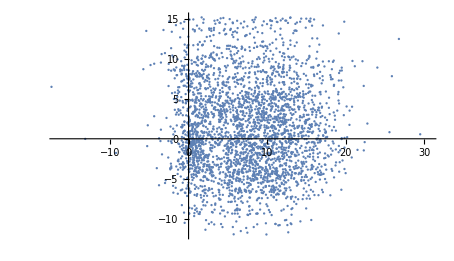

```mathematica
ListPlot[Function[obv,
AstronomicalPosition[obv["ObjectB"],obv["Date"]]-AstronomicalPosition[obv["ObjectA"],obv["Date"]]
]/@Select[grasshoffObservations,#["Type"]==="RelativePosition"&],AspectRatio->Automatic]
```

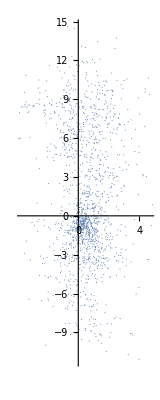

```mathematica
ListPlot[Function[obv,
AstronomicalPosition[obv["ObjectB"],obv["Date"]]-AstronomicalPosition[obv["ObjectA"],obv["Date"]]
]/@Select[jonesObservations,#["Type"]==="RelativePosition"&],AspectRatio->Automatic]
```

## Basic analysis

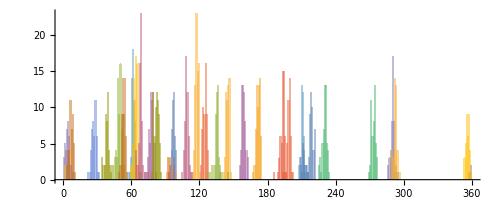

```mathematica
Histogram[KeyValueMap[Tooltip[#2,#1]&]@Merge[Function[obv,
obv["ObjectB"]->AstronomicalPosition[obv["ObjectA"],obv["Date"]][[1]]
]/@Select[jonesObservations,#["Type"]==="RelativePosition"&],Identity],{1},AspectRatio->Automatic]
```

## Questions